### Computing the Numerical profile

```mathematica
Quit[]
```

```mathematica
Dgg=gg'[r]==(-2 c Mp w^2 gg[r]^5 ϕ[r]^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2-2 c Mp gg[r]^3 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2 (-w^2 ϕ[r]^2+NN[r]^2 ϕ'[r]^2)+Λ^3 gg[r]^3 (r^2 w^2 ϕ[r]^2+NN[r]^2 (-Mp^2+m^2 r^2 ϕ[r]^2)) (w^2 gg[r]^3 ϕ[r]^2-gg[r] NN[r]^2 ϕ'[r]^2)^2+Λ^3 gg[r] NN[r]^2 (Mp^2+r^2 ϕ'[r]^2) (w^2 gg[r]^3 ϕ[r]^2-gg[r] NN[r]^2 ϕ'[r]^2)^2-2 d Mp gg[r] NN[r]^6 ϕ'[r]^5 (ϕ'[r]+4 r ϕ''[r])-2 c Mp gg[r] NN[r]^2 ϕ'[r] (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2 (ϕ'[r]+4 r ϕ''[r])-4 d Mp r w^2 gg[r]^3 NN[r]^4 ϕ[r] ϕ'[r]^3 (3 ϕ'[r]^2-5 ϕ[r] ϕ''[r])+2 d Mp w^4 gg[r]^5 NN[r]^2 ϕ[r]^3 ϕ'[r] (-2 r ϕ'[r]^2+ϕ[r] (ϕ'[r]+2 r ϕ''[r])))/(4 d Mp r w^4 gg[r]^4 NN[r]^2 ϕ[r]^4 ϕ'[r]^2+24 d Mp r w^2 gg[r]^2 NN[r]^4 ϕ[r]^2 ϕ'[r]^4-12 d Mp r NN[r]^6 ϕ'[r]^6+4 c Mp r w^2 gg[r]^2 ϕ[r]^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2-12 c Mp r NN[r]^2 ϕ'[r]^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2+2 Λ^3 Mp^2 r NN[r]^2 (w^2 gg[r]^3 ϕ[r]^2-gg[r] NN[r]^2 ϕ'[r]^2)^2);

DNN=NN'[r]==(NN[r] (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2) (w^2 gg[r]^6 ϕ[r]^2 ((-2 c Mp+Λ^3 r^2) w^2 ϕ[r]^2+Λ^3 NN[r]^2 (Mp-m r ϕ[r]) (Mp+m r ϕ[r]))-6 (c+d) Mp NN[r]^4 ϕ'[r]^4+gg[r]^4 (-Λ^3 Mp^2 w^2 NN[r]^2 ϕ[r]^2+Λ^3 NN[r]^4 (-Mp^2+m^2 r^2 ϕ[r]^2) ϕ'[r]^2+2 c Mp w^4 ϕ[r]^3 (ϕ[r]+4 r ϕ'[r]))+gg[r]^2 NN[r]^2 ϕ'[r] (NN[r]^2 ϕ'[r] (Λ^3 Mp^2+(2 c Mp-Λ^3 r^2) ϕ'[r]^2)+2 Mp w^2 ϕ[r] (ϕ'[r] ((2 c+d) ϕ[r]-2 (2 c+3 d) r ϕ'[r])+2 d r ϕ[r] ϕ''[r]))))/(2 Mp r (gg[r]^6 (Λ^3 Mp w^4 NN[r]^2 ϕ[r]^4+2 c w^6 ϕ[r]^6)-2 w^2 gg[r]^4 NN[r]^2 ϕ[r]^2 (Λ^3 Mp NN[r]^2+(5 c-d) w^2 ϕ[r]^2) ϕ'[r]^2+gg[r]^2 NN[r]^4 (Λ^3 Mp NN[r]^2+2 (7 c+6 d) w^2 ϕ[r]^2) ϕ'[r]^4-6 (c+d) NN[r]^6 ϕ'[r]^6));

DDPhi=ϕ''[r]==(w^6 gg[r]^11 ((-2 c Mp+Λ^3 r^2) w^2-Λ^3 m^2 r^2 NN[r]^2) ϕ[r]^7+6 (c+d) Mp NN[r]^7 gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]^7-w^6 gg[r]^8 ϕ[r]^6 gg'[r] (4 c Mp r w^2 ϕ[r]+(-2 c Mp+Λ^3 r^2) NN[r]^2 ϕ'[r])+w^4 gg[r]^9 ϕ[r]^5 (2 c Mp w^4 ϕ[r]^2+w^2 NN[r] ϕ[r] (2 Λ^3 r NN[r]+(-2 c Mp+Λ^3 r^2) NN'[r]) ϕ'[r]+3 NN[r]^2 ((2 c Mp-Λ^3 r^2) w^2+Λ^3 m^2 r^2 NN[r]^2) ϕ'[r]^2)+w^2 gg[r]^4 NN[r]^3 ϕ[r]^2 ϕ'[r]^3 (4 (9 c+13 d) Mp r w^2 ϕ[r]^2 gg'[r] NN'[r]+3 (2 c Mp-Λ^3 r^2) NN[r]^3 gg'[r] ϕ'[r]^2+2 Mp w^2 NN[r] ϕ[r] (-2 (3 c+8 d) r gg'[r] ϕ'[r]+ϕ[r] (3 (3 c+d) gg'[r]-2 d r gg''[r])))+gg[r]^2 NN[r]^5 ϕ'[r]^5 (-4 (9 c+10 d) Mp r w^2 ϕ[r]^2 gg'[r] NN'[r]+(-2 c Mp+Λ^3 r^2) NN[r]^3 gg'[r] ϕ'[r]^2-2 Mp w^2 NN[r] ϕ[r] (-(2 c+7 d) r gg'[r] ϕ'[r]+ϕ[r] ((9 c+7 d) gg'[r]-d r gg''[r])))+w^4 gg[r]^6 NN[r] ϕ[r]^4 ϕ'[r] (4 (-3 c+2 d) Mp r w^2 ϕ[r]^2 gg'[r] NN'[r]+3 (-2 c Mp+Λ^3 r^2) NN[r]^3 gg'[r] ϕ'[r]^2+2 Mp w^2 NN[r] ϕ[r] (3 (2 c+3 d) r gg'[r] ϕ'[r]+ϕ[r] ((-3 c+d) gg'[r]+d r gg''[r])))-2 Mp gg[r] NN[r]^6 ϕ'[r]^5 (2 d r w^2 ϕ[r]^2 gg'[r]^2+(c+d) NN[r] ϕ'[r]^2 (3 NN'[r]+2 r NN''[r]))-w^2 gg[r]^7 NN[r] ϕ[r]^3 ϕ'[r] (6 Mp w^4 ϕ[r]^2 ((c+d) NN[r]+d r NN'[r]) ϕ'[r]+w^2 NN[r] ϕ[r] (-4 d Mp r w^2+6 Λ^3 r NN[r]^2+3 (-2 c Mp+Λ^3 r^2) NN[r] NN'[r]) ϕ'[r]^2+3 NN[r]^3 ((2 c Mp-Λ^3 r^2) w^2+Λ^3 m^2 r^2 NN[r]^2) ϕ'[r]^3+2 Mp w^4 ϕ[r]^3 ((-3 c+d) NN'[r]+(-2 c+d) r NN''[r]))+gg[r]^5 NN[r]^2 ϕ[r] ϕ'[r] (-8 d Mp r w^6 ϕ[r]^5 gg'[r]^2+2 Mp w^4 NN[r] ϕ[r]^2 ((3 c+8 d) NN[r]+12 d r NN'[r]) ϕ'[r]^3+3 w^2 NN[r]^3 ϕ[r] (2 Λ^3 r NN[r]+(-2 c Mp+Λ^3 r^2) NN'[r]) ϕ'[r]^4+NN[r]^4 ((2 c Mp-Λ^3 r^2) w^2+Λ^3 m^2 r^2 NN[r]^2) ϕ'[r]^5-2 Mp w^4 ϕ[r]^3 ϕ'[r]^2 (14 d r NN'[r]^2+NN[r] ((9 c+7 d) NN'[r]+2 (3 c+2 d) r NN''[r])))+gg[r]^3 NN[r]^4 ϕ'[r]^3 (12 d Mp r w^4 ϕ[r]^4 gg'[r]^2-2 Mp w^2 NN[r] ϕ[r] ((c+5 d) NN[r]-7 d r NN'[r]) ϕ'[r]^3-NN[r]^2 (4 d Mp r w^2+2 Λ^3 r NN[r]^2+(-2 c Mp+Λ^3 r^2) NN[r] NN'[r]) ϕ'[r]^4+2 Mp w^2 ϕ[r]^2 ϕ'[r]^2 (-2 d r NN'[r]^2+NN[r] ((9 c+11 d) NN'[r]+(6 c+7 d) r NN''[r]))))/(gg[r] NN[r] ((2 c Mp-Λ^3 r^2) w^6 gg[r]^8 NN[r] ϕ[r]^6-2 d Mp r w^6 gg[r]^5 NN[r] ϕ[r]^6 gg'[r]+2 d Mp r w^2 gg[r] NN[r]^5 ϕ[r]^2 gg'[r] ϕ'[r]^4+2 (c+d) Mp NN[r]^6 (NN[r]+2 r NN'[r]) ϕ'[r]^6+w^2 gg[r]^4 NN[r]^2 ϕ[r]^2 ϕ'[r]^2 (12 (c+3 d) Mp r w^2 ϕ[r]^2 NN'[r]+3 (2 c Mp-Λ^3 r^2) NN[r]^3 ϕ'[r]^2+2 Mp w^2 NN[r] ϕ[r] (3 (c+d) ϕ[r]-8 d r ϕ'[r]))+w^4 gg[r]^6 ϕ[r]^4 (2 (-2 c+d) Mp r w^2 ϕ[r]^2 NN'[r]+3 (-2 c Mp+Λ^3 r^2) NN[r]^3 ϕ'[r]^2-2 Mp w^2 NN[r] ϕ[r] (c ϕ[r]-6 d r ϕ'[r]))-gg[r]^2 NN[r]^4 ϕ'[r]^4 (2 (6 c+5 d) Mp r w^2 ϕ[r]^2 NN'[r]+(2 c Mp-Λ^3 r^2) NN[r]^3 ϕ'[r]^2+2 Mp w^2 NN[r] ϕ[r] (3 c ϕ[r]+4 d ϕ[r]-2 d r ϕ'[r]))));
```

```mathematica
SeidelEqsList={};
SeidelEqsListH={};
SeidelBCList={};
SeidelBCListH={};
SeidelCoefFunctionsList={};
AppendTo[SeidelEqsList,{DDPhi,DNN,Dgg}];

AppendTo[SeidelCoefFunctionsList,{NN,NN',gg,gg',φ,NN''}];

AppendTo[SeidelBCList,{NN[rMin]==N0,gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0,NN'[rMin] ==0, gg'[rMin] == 0}];
```

```mathematica
SeidelBCList
```

{{NN[rMin]==N0,gg[rMin]==1.,φ[rMin]==ϕ0,φ'[rMin]==0,NN'[rMin]==0,gg'[rMin]==0}}

#### Test

```mathematica
Etam03={{0.015,1.0528621673583980,30},{0.02,1.0723885893821720,30},{0.03,1.1145928651094440,30},{0.04,1.1613612586750880,30},{0.042,1.1713035509047010,25},{0.044,1.1814513386399140,30},{0.046,1.1918086057616720,30},{0.048,1.2023797700315790,30},{0.05,1.2131691131351870,30},{0.052,1.224180970558401000,30},{0.054,1.2354198299260930,30},{0.056,1.246890453211968000,30},{0.058,1.258597242059905000,22},{0.06,1.2705452417886480,30},{0.07,1.334076062600186000,18},{0.08,1.404409375520368000,17},{0.09,1.482261297866646000,18},{0.1,1.568426066103807000,20}};
```

```mathematica
{0.054,1.242757501645907,30,30,0,10^-8},{0.11, 1.718127868315551900,20,-0.07,10^-4},{0.08,1.40440709375520368000,20,30,-0.3,10^-4},{0.09,1.47716891064615166,20,30,-0.4,10^-4},{0.10,1.563466198607706237,20,30,-0.5,10^-4},{0.102,1.6445553340031241,19,-0.8,10^-4},{0.1,1.681199074413719,20,30,-0.95,10^-4,0.562769635014356},{0.1,1.6976746558,20,30,-0.98,10^-4,0.553920067082275}{0.1,1.709443707626451870,12,30,-1,10^-4},{0.1,1.709442971786451870,28,25,-1,10^-4,0.547918118298546}
```

```mathematica
{0.08,1.8340966531827487962,20,-2,10^-1} ,{0.07,1.52501301804375,19,-2,10^-4}
```

```mathematica
η=-1;
c4=0;d4=0; (*1/2*)
L3=(1/Abs[η])^(1/3);
Mp=1;mS=1;N0=1;
rMin=10^-8;(*10^-8,10^-4*)
rMax=30;
ϕ0=0.054*√(8π);
 w=1.242757501645907;(*1.709442971786451870*)(*1.52501301820100283;*)

s1=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

{{NN→InterpolatingFunction[…],NN'→InterpolatingFunction[…],gg→InterpolatingFunction[…],gg'→InterpolatingFunction[…],φ→InterpolatingFunction[…],NN''→InterpolatingFunction[…]}}

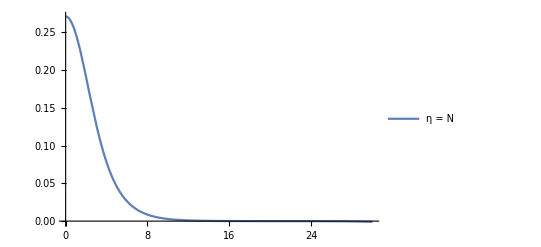

```mathematica
Plot[{Evaluate[φ[r]/.s1]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = N", "η = Sc","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],PlotRange->All]
```

```mathematica
M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)/.s1]8π;
```

```mathematica
M[rMax]
M95=Last[M[rMax]]*0.95
r95=FindRoot[M[r]==M95,{r,rMin,rMax}][[1,2]]
```

{15.9326}

15.1359

6.04864

```mathematica
B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s1]*Evaluate[gg[rMax]/.s1]==1,C],{18,17}];
w2=w*B[[1,1,1,2]]
```

0.853159

```mathematica
(* Solving again *)
SeidelBCList={};
Clear[ w,N0];

AppendTo[SeidelBCList,{NN[rMin]==N0,gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0,NN'[rMin] ==0, gg'[rMin] == 0}];
```

```mathematica
N0= B[[1,1,1,2]];
w=w2;(*w2 0.770583661709725143*)(*0.547918118298546*)
rMax=18;(*18*) (*0.547918118298546*)(*0.466937349601346987, 0.46685434353982*)
s1=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

{{NN→InterpolatingFunction[…],NN'→InterpolatingFunction[…],gg→InterpolatingFunction[…],gg'→InterpolatingFunction[…],φ→InterpolatingFunction[…],NN''→InterpolatingFunction[…]}}

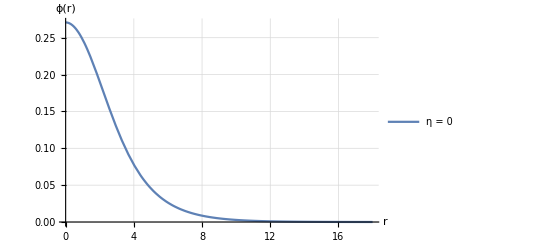

```mathematica
Plot[{Evaluate[φ[r]/.s1]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = 0"(*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic,AxesOrigin->{0,0}]
```

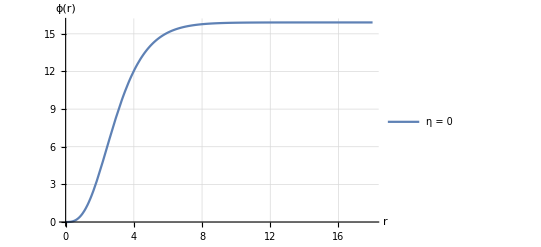

```mathematica
Plot[{Evaluate[M[r]/.s1]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = 0"(*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic,AxesOrigin->{0,0}]
```

```mathematica
Masa=M[rMax]
fun[r_]:=√(1-Masa/(4 π r));  gfun[r_]:=√((1-Masa/(4 π r))^-1);dNfun[r_]:=Masa/(8π √(1-Masa/(4π r)) r^2); dgfun[r_]:=-(Masa (1/(1-Masa/(4π r)))^(3/2))/(8π r^2); ddNfun[r_]:=(Masa (3 Masa-16 π r))/(8 √π √(4 π-Masa/r) r^3 (-Masa+4 π r));
```

{15.909}

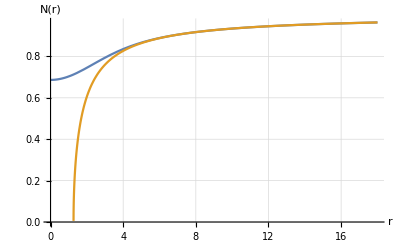

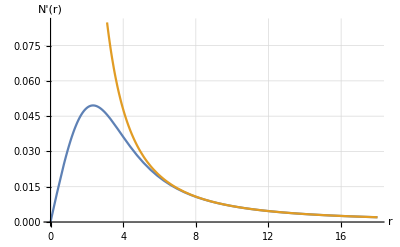

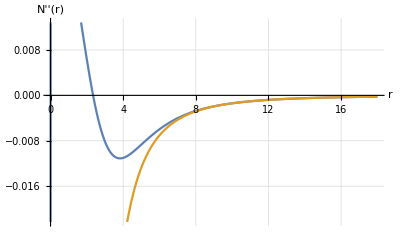

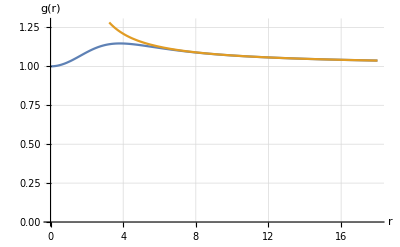

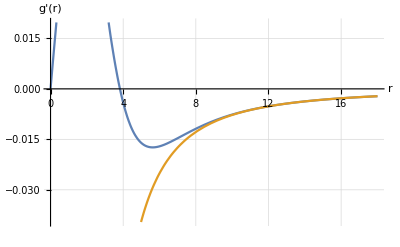

```mathematica
Plot[{Evaluate[NN[r]/.s1],fun[r]},{r,rMin,rMax},
Background->White,
PlotRange->Automatic,AxesLabel->{"r","N(r)"},
GridLines->Automatic,AxesOrigin->{0,0}]

Plot[{Evaluate[NN'[r]/.s1], dNfun[r]},{r,rMin,rMax},
Background->White,
PlotRange->Automatic,AxesLabel->{"r","N'(r)"},
GridLines->Automatic,AxesOrigin->{0,0}]

Plot[{Evaluate[NN''[r]/.s1], ddNfun[r]},{r,rMin,rMax},
Background->White,
PlotRange->Automatic,AxesLabel->{"r","N''(r)"},
GridLines->Automatic,AxesOrigin->{0,0}]

Plot[{Evaluate[gg[r]/.s1],gfun[r]},{r,rMin,rMax},
Background->White,
PlotRange->Automatic,AxesLabel->{"r","g(r)"},
GridLines->Automatic,AxesOrigin->{0,0}]

Plot[{Evaluate[gg'[r]/.s1], dgfun[r]},{r,rMin,rMax},
Background->White,
PlotRange->Automatic,AxesLabel->{"r","g'(r)"},
GridLines->Automatic,AxesOrigin->{0,0}]
```

```mathematica
isco[r_]:=Evaluate[NN[r]-r NN'[r]/.s1]
```

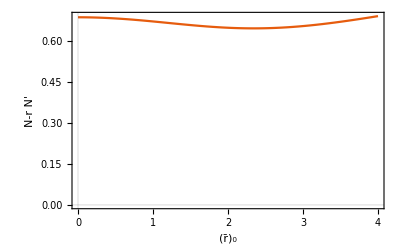

```mathematica
Plot[isco[r],{r,rMin,4},AxesOrigin->{0,0},PlotTheme->"Scientific",FrameLabel->{"(r̄)_0","N-r N'"},ImageSize->400(*,PlotRange->{{2,3},{-0.1,0.1}}*)]
```

```mathematica
D[Sqrt[(r^3 NN'[r])/(NN[r]-r NN'[r])],r]//Simplify
```

(r^2 (-3 r NN'[r]^2+NN[r] (3 NN'[r]+r NN''[r])))/(2 √((r^3 NN'[r])/(NN[r]-r NN'[r])) (NN[r]-r NN'[r])^2)

```mathematica
profL[r_]:=Sqrt[Evaluate[(r^3 NN'[r])/(NN[r]-r NN'[r])/.S]]
dprofL[r_]:=Evaluate[(r^2 (-3 r NN'[r]^2+NN[r] (3 NN'[r]+r NN''[r])))/(2 √((r^3 NN'[r])/(NN[r]-r NN'[r])) (NN[r]-r NN'[r])^2)/.S]
```

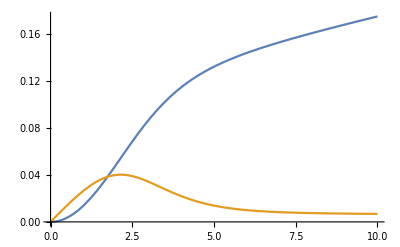

```mathematica
Plot[{profL[r]/Masa,dprofL[r]/Masa},{r,rMin, 10},PlotRange->Automatic]
```

```mathematica
FindRoot[isco[r]==0,{r,2.9,3}]
```

{r→2.9579}

```mathematica
2.6517363030065955/rs
```

1.20567

```mathematica
2.957902654411634/rs
```

1.34487

```mathematica
r2.199395755115796`
```

```mathematica
Datf={};
Do[
AppendTo[Datf,{r/rs,isco[r][[1]]}],
{r,rMin,rMax,0.005}
]
```

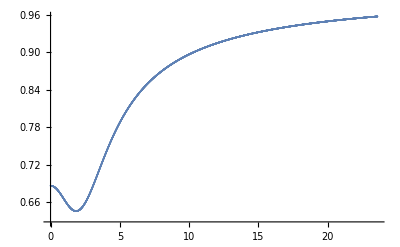

```mathematica
ListPlot[Datf]
```

```mathematica
Export["PS_L3_0.dat",Datf]
```

PS_L3_0.dat

```mathematica
dat={};
Do[AppendTo[dat,{r/rs,isco[r][[1]]/rs}],{r,rMin,rMax,0.05}]
```

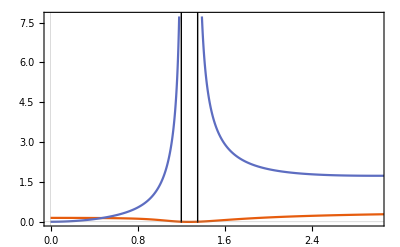

```mathematica
line1=Line[{{1.2,-0.03},{1.2,8}}];
line2=Line[{{1.35,-0.03},{1.35,8}}];

ListPlot[{dat,dat2},PlotTheme->"Scientific",Joined->True,PlotRange->{{0,3},Automatic},
Epilog->{line1,line2}]
```

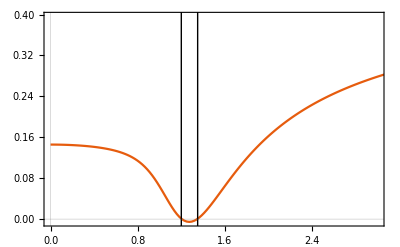

```mathematica
line1=Line[{{1.2,-0.03},{1.2,8}}];
line2=Line[{{1.35,-0.03},{1.35,8}}];

ListPlot[{dat},PlotTheme->"Scientific",Joined->True,PlotRange->{{0,3},Automatic},
Epilog->{line1,line2}]
```

```mathematica
FindRoot[isco[r],{r,2.5,2.7}]
```

{r→2.65174}

## Acretion

```mathematica
(*interpolando Schw*)
fun[r_]:=√(1-Masa/(4 π r));  gfun[r_]:=√((1-Masa/(4 π r))^-1); dNfun[r_]:=Masa/(8π √(1-Masa/(4π r)) r^2); ddNfun[r_]:=(Masa (3 Masa-16 π r))/(8 √π √(4 π-Masa/r) r^3 (-Masa+4 π r));dgfun[r_]:=-(Masa (1/(1-Masa/(4π r)))^(3/2))/(8π r^2);
datg={};
datN={};
datdg={};
datdN={};
datddN={};
Do[
AppendTo[datg,{r,Last[ gfun[r]]}];
AppendTo[datN,{r,Last[ fun[r]]}];
AppendTo[datdg,{r,Last[dgfun[r]]}];
AppendTo[datdN,{r,Last[ dNfun[r]]}];
AppendTo[datddN,{r,Last[ ddNfun[r]]}];
,{r, rMax-5,60Masa[[1]],0.5}
]

intgS=Interpolation[datg]/.Equal-> Rule;
intNS=Interpolation[datN]/.Equal-> Rule;
intdgS=Interpolation[datdg]/.Equal-> Rule;
intdNS=Interpolation[datdN]/.Equal-> Rule;
intddNS=Interpolation[datddN]/.Equal-> Rule;
```

```mathematica
(* Definiendo de la métrica *)
S[r_]:= {NN->Piecewise[{{s1[[1,1,2]],r<=rMax},{intNS,r>rMax}}], gg-> Piecewise[{{s1[[1,3,2]],r<=rMax},{ intgS,r>rMax}}],NN'->Piecewise[{{s1[[1,2,2]],r<=rMax},{ intdNS,r>rMax}}],gg'-> Piecewise[{{s1[[1,4,2]],r<=rMax},{intdgS,r>rMax}}],NN''->Piecewise[{{s1[[1,6,2]],r<=rMax},{ intddNS,r>rMax}}]}
```

```mathematica
datn={};
datgg={};
Do[
AppendTo[datn,{r,Evaluate[NN[r]/.S]}];
AppendTo[datgg,{r,Evaluate[gg[r]/.S]}];
,{r, rMin,30Masa[[1]]/(8π),0.01}
]
```

```mathematica
Export["N_profile_L3_1.dat",datn]
Export["g_profile_L3_1.dat",datgg]
```

N_profile_L3_1.dat

g_profile_L3_1.dat

#### python

```mathematica
datn={};
datdn={};
datddn={};
datG={};
datdG={};
Do[
AppendTo[datn,{r,Evaluate[NN[r]]/.S}];
AppendTo[datdn,{r,Evaluate[NN'[r]]/.S}];
AppendTo[datddn,{r,Evaluate[NN''[r]]/.S}];
AppendTo[datG,{r,Evaluate[gg[r]]/.S}];
AppendTo[datdG,{r,Evaluate[gg'[r]]/.S}],
{r,rMin,60Masa[[1]],0.05}
]
Export["N_profile.dat",datn]
Export["dN_profile.dat",datdn]
Export["ddN_profile.dat",datddn]
Export["g_profile.dat",datG]
Export["dg_profile.dat",datdG]
```

InterpolatingFunction::dmval: Input value {958.55} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

N_profile.dat

dN_profile.dat

ddN_profile.dat

g_profile.dat

dg_profile.dat

```mathematica
a=ListPlot[datddn,PlotRange->{{0,50},All}];
b=Plot[Evaluate[NN''[r]/.S],{r,rMin,50},PlotRange->{{0,50},All}];
Show[{a,b}]
```

```mathematica
Masa/(8π)
```

{0.635856}

#### masa

```mathematica
Solve[(5.31*Masa/(8π))/m6*10^-12==3*10^9,m6]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{m6→1.12546×10^-21}}

```mathematica
(*masa en unidades físicas *)
```

```mathematica
m4=1.20*10^-18(*eV*);
```

```mathematica
m4=2.51*10^-13(*eV*);
Masa2=0.473 (* mpl^2/m*);
```

```mathematica
Mf=(5.31*Masa2)/m4*10^-12(* masas solares *)
MfInc=(5.31*Masa2 *8π)/m4*10^-12(* masas solares *)
```

10.0065

251.491

```mathematica
Mobj=3*10^9;
```

#### acrecion

```mathematica
(*
Calculando el flujo electromagnético ; 
arxiv: 1009.1250v1
*)
```

```mathematica
ClearAll[Ω,dΩ,EE,L,dL,f,T,fluj,r0,Rout]
```

```mathematica
f[R_?NumberQ,ri_?NumberQ]:=Module[{Rv=N@R,r0=N@ri, dΩ, Ω, EE, L,dL,term, flujo},

ClearAll[flujo,Ω,dΩ,EE,L,dL,term];
Ω[r_]:=Evaluate[(√(r NN[r] NN'[r]))/r/.S[r]];
dΩ[r_]:=Evaluate[(r NN'[r]^2+NN[r] (-NN'[r]+r NN''[r]))/(2 r √(r NN[r] NN'[r]))/.S[r]];
EE[r_]:=Evaluate[NN[r]^2/(√(NN[r] (NN[r]-r NN'[r])))/.S[r]];
L[r_]:=Evaluate[(r √(r NN[r] NN'[r]))/(√(NN[r] (NN[r]-r NN'[r])))/.S[r]];

dL[r_]:=Evaluate[(r NN[r]^2 (-3 r NN'[r]^2+NN[r] (3 NN'[r]+r NN''[r])))/(2 √(r NN[r] NN'[r]) (NN[r] (NN[r]-r NN'[r]))^(3/2))/.S[r]];

term[r_]:=Evaluate[1/(NN[r]gg[r])/.S[r]];

flujo=-1.4556*10^18(Mpunt*m^2)/(4π Rv)(term[Rv])dΩ[Rv]/(EE[Rv]-L[Rv] Ω[Rv])^2 NIntegrate[(EE[rB]-L[rB] Ω[rB])dL[rB],{rB,r0,Rv},Method->{Automatic,"SymbolicProcessing"->0},MaxRecursion->20];

Return[flujo] (* erg s^-1 cm^-2*)
]
```

```mathematica
(* Calculando la temperatura F(R)=σ T(R)^4  *)
```

```mathematica
T[R_?NumberQ,ri_?NumberQ]:= Module[{Rv=N@R,r0=N@ri,Temp},
ClearAll[Temp];
Temp=(1/σ f[Rv,r0])^(1/4);
Return[Temp] (*K*);
];
```

```mathematica
(* Calculando el flujo electromagnético *)
```

```mathematica
fluj[ν_?NumberQ,ri_?NumberQ]:=Module[{v=N@ν,r0=N@ri, lumin, term2},
ClearAll[lumin];
term2[r_]:=Evaluate[NN[r]gg[r]/.S[r]];
lumin=4.5329*10^-17 ν^3 m^-2 Cos[i]NIntegrate[(r term2[r])/(Exp[(h ν)/(kk T[r,r0])]-1),{r,r0,Rout},MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0}];
Return[lumin]
]
```

```mathematica
(*ISCO[r0_?NumberQ,M_?NumberQ]:=Module[{r=N@r0,m=N@M, x,y,eq,dN,n},
L[r_]:=Evaluate[(r √(r NN[r] NN'[r]))/(√(NN[r] (NN[r]-r NN'[r])))/.S];
y=L[r]/m;
x=r/m;

dN[r_]:=Evaluate[(NN'[r]/.S)];
n[r_]:=Evaluate[(NN[r]/.S)];

eq=r dN[r]((L[r]/r)^2+1)-(L[r]/r)^2 n[r];
If[
eq≤ 10^-5&&eq≥ 0, Return[{{x, y},1}],Return[{{0, 0},0}]]
]*)
```

```mathematica
profL[r_]:=Sqrt[Evaluate[(r^3 NN'[r])/(NN[r]-r NN'[r])/.S]]
```

#### draft

```mathematica
(* via paper *)
```

#### luminosidad

```mathematica
rs=(2* Masa[[1]])/(8π)
```

2.19913

```mathematica
dat2={};
Do[
AppendTo[dat2,{r/rs,profL[r]/rs}],{r,rMin, 100,0.005}
]
```

```mathematica
Export["HL3_2_42.dat",dat]
```

HL3_2_42.dat

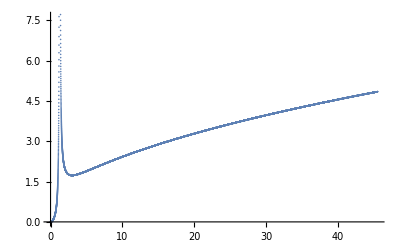

```mathematica
ListPlot[dat2]
```

#### acreción

```mathematica
Mf=(5.31*Masa)/m4*10^-12;(* masas solares *)
Mobj=3*10^9;
```

```mathematica
NSolve[Mf==Mobj,m4]
```

{{m4→2.81589×10^-20}}

```mathematica
rs=(2* Masa[[1]])/(8π)
```

1.266

```mathematica
m=4.89141*10^-1(*10^-19 eV*);
Mpunt=2*10^-6 (* Masa Solares * year^-1 *);
i=0;
ri=3.01*rs  (* 3.01*rs *) (* 6 Masa  6 Masa[[1]]/(8*Pi)*);
σ=5.67×10^-5 (* erg s^-1 cm^-2 K^-4 *);
h=6.6256*10^-27(* erg s *);
kk=1.3805*10^-16(* erg K^-1 *);
νMin=10(*1*10^10*);
νMax=20(*10^18*);
Rout=50*Masa[[1]] (*500rs*)
```

795.448

```mathematica
(*3.1, 4.1, 5.1, 10.1, 20.1, 30.1, 40.1, 50*)
```

```mathematica
Datf={};
DatT={};
Do[
AppendTo[Datf,{r,f[r,ri]}];
AppendTo[DatT,{r,T[r,ri]}],
{r,ri,Rout,0.5}
]
```

```mathematica
valuesr=N[10^Subdivide[Log10[ri],Log10[Rout],600]];
```

```mathematica
Datf={};
(*DatT2={};*)
Do[
r=valuesr[[i]];
AppendTo[Datf,{r/rs,f[r,ri]/Mpunt}];
(*AppendTo[DatT2,{r,T[r,ri]}]*),
{i,1,Length[valuesr]}
]
```

```mathematica
Export["T799rs_L3_Inf.dat",DatT2]
```

T799rs_L3_Inf.dat

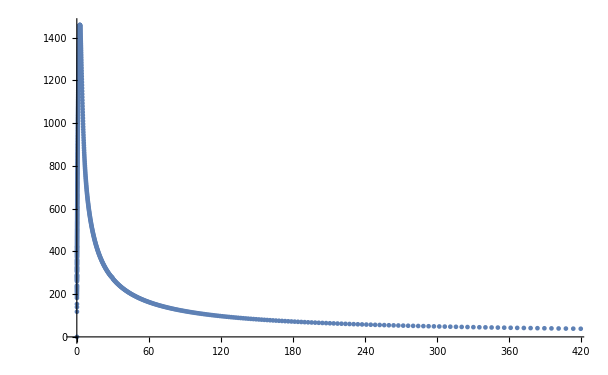

```mathematica
ListPlot@DatT2
```

```mathematica
(*ListPlot[Datf,PlotRange->All,Joined->False,PlotTheme->"Scientific"]*)
ListLogPlot[DatT/100,PlotRange->{{0,6},All},Joined->True,PlotTheme->"Scientific"]
```

```mathematica
values=N[10^Subdivide[8,15,300]];(*,νMin,νMax*)

Dat={};
Do[
ν=values[[ii]];
lum=ν fluj[ν,ri];
AppendTo[Dat,{ν,lum}],{ii,1,Length[values]}
]
```

$Aborted

```mathematica
Dat
```

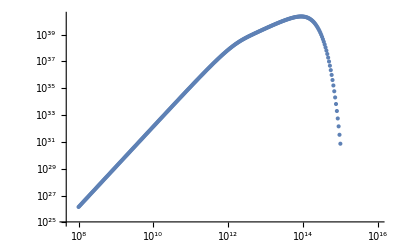

```mathematica
ListLogLogPlot[Dat,PlotRange->{{0,10^16},Automatic}]
```

```mathematica
Export["F628rs_L3_1.dat",Dat]
```

F628rs_L3_1.dat

```mathematica
Export["HS1.dat",Dat]
```

HS1.dat

```mathematica
Dat2=Dat;
```

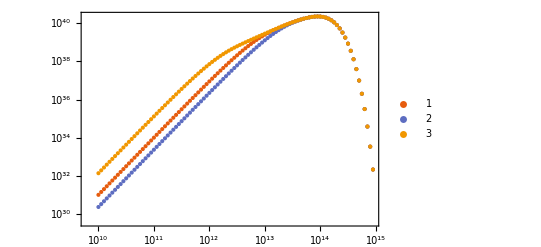

```mathematica
ListLogLogPlot[{dat100[[;;100]],dat32[[;;100]],dat799[[;;100]]},PlotLegends->Automatic,PlotTheme->"Scientific"]
```

#### Ejemplo Caso A paper

```mathematica
m=8.485805016294589*10^7(*2.51*10^6(*10^-19 eV*)*);
Mpunt=2*10^-6 (* Masa Solares * year^-1 *);
i=π/3;
ri=0.025 (*rMin*) (* 6 Masa  *);
σ=5.67×10^-5 (* erg s^-1 cm^-2 K^-4 *);
h=6.6256*10^-27(* erg s *);
kk=1.3805*10^-16(* erg K^-1 *);
νMin=10(*1*10^10*);
νMax=20(*10^18*);
Rout=50*Masa[[1]]/(8π)
```

31.7928

```mathematica
Datf={};
DatT={};
Do[
AppendTo[Datf,{r,f[r,ri]}];
AppendTo[DatT,{r,T[r,ri]}],
{r,ri,Rout,0.005}
]
```

-Graphics-

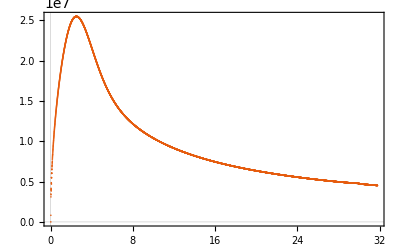

```mathematica
ListPlot[Datf,PlotRange->All,Joined->False,PlotTheme->"Scientific"]
ListPlot[DatT,PlotRange->All,Joined->False,PlotTheme->"Scientific"]
```

```mathematica
values=N[10^Subdivide[νMin,νMax,100]];

Dat={};
Do[
ν=values[[ii]];
lum=ν fluj[ν,ri];
AppendTo[Dat,{ν,lum}],{ii,1,Length[values]}
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

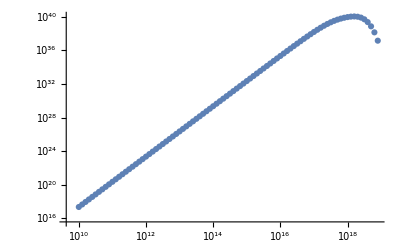

```mathematica
ListLogLogPlot@Dat[[;;90]]
```

#### Schw

```mathematica
Quit[]
```

```mathematica
(*interpolando Schw*)
metricSchw={ NN[r]-> √(1-Masa/(4 π r)),  gg[r]-> √((1-Masa/(4 π r))^-1),NN'[r]-> Masa/(8π √(1-Masa/(4π r)) r^2), NN''[r]-> (Masa (3 Masa-16 π r))/(8 √π √(4 π-Masa/r) r^3 (-Masa+4 π r)),gg'[r]-> -(Masa (1/(1-Masa/(4π r)))^(3/2))/(8π r^2)};
```

```mathematica
ClearAll[Ω,dΩ,EE,L,dL,f,T,fluj,r0,Rout]
f[R_?NumberQ,ri_?NumberQ]:=Module[{Rv=N@R,r0=N@ri},

ClearAll[flujo,Ω,dΩ,EE,L,dL,term];
Ω[r_]:=Evaluate[((√(r NN[r] NN'[r]))/r/.metricSchw)//Simplify];
dΩ[r_]:=Evaluate[((r NN'[r]^2+NN[r] (-NN'[r]+r NN''[r]))/(2 r √(r NN[r] NN'[r]))/.metricSchw)//Simplify];
EE[r_]:=Evaluate[(NN[r]^2/(√(NN[r] (NN[r]-r NN'[r])))/.metricSchw)//Simplify];
L[r_]:=Evaluate[((r √(r NN[r] NN'[r]))/(√(NN[r] (NN[r]-r NN'[r])))/.metricSchw)//Simplify];

dL[r_]:=Evaluate[((r NN[r]^2 (-3 r NN'[r]^2+NN[r] (3 NN'[r]+r NN''[r])))/(2 √(r NN[r] NN'[r]) (NN[r] (NN[r]-r NN'[r]))^(3/2))/.metricSchw)//Simplify];

term[r_]:=Evaluate[(NN[r]/gg[r]/.metricSchw)//Simplify];

flujo=-1.4556*10^18(Mpunt*m^2)/(4π Rv)dΩ[Rv]/(EE[Rv]-L[Rv] Ω[Rv])^2 NIntegrate[(EE[rB]-L[rB] Ω[rB])dL[rB],{rB,r0,Rv},Method->{Automatic,"SymbolicProcessing"->0},MaxRecursion->20](term[Rv]);

Return[flujo] (* erg s^-1 cm^-2*)
]
(* Calculando la temperatura F(R)=σ T(R)^4  *)
T[R_?NumberQ,ri_?NumberQ]:= Module[{Rv=N@R,r0=N@ri},
ClearAll[Temp];
Temp=(1/σ f[Rv,r0])^(1/4);
Return[Temp] (*K*);
];
(* Calculando el flujo electromagnético *)
fluj[ν_?NumberQ,ri_?NumberQ]:=Module[{v=N@ν,r0=N@ri},
ClearAll[lumin];
lumin=4.5329*10^-17 ν^3 m^-2 Cos[i]NIntegrate[r/(Exp[(h ν)/(kk T[r,r0])]-1),{r,r0,Rout},MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0}];
Return[lumin]
]
```

```mathematica
ISCO[r0_?NumberQ,M_?NumberQ]:=Module[{r=N@r0,m=N@M, x,y,eq,dN,n},
L[r_]:=Evaluate[((r √(r NN[r] NN'[r]))/(√(NN[r] (NN[r]-r NN'[r])))/.metricSchw)//Simplify];
y=L[r]/m;
x=r/m;

dN[r_]:=Evaluate[(NN'[r]/.metricSchw)];
n[r_]:=Evaluate[(NN[r]/.metricSchw)];

eq=r dN[r]((L[r]/r)^2+1)-(L[r]/r)^2 n[r];
If[
eq≤ 10^-5&&eq≥ 0, Return[{x, y}],Return[{0, 0}]]
]
```

```mathematica
profL[r_]:=Evaluate[(Sqrt[(r^3 NN'[r])/(NN[r]-r NN'[r])/.metricSchw])//Simplify]
```

```mathematica
test={};
Do[
t=ISCO[i,Masa];
AppendTo[test,t],{i,10^-3, 100,0.5}
]
```

```mathematica
test
```

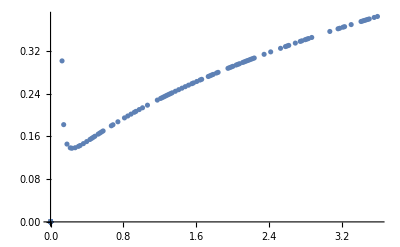

```mathematica
ListPlot[test,Joined->False]
```

```mathematica
test
```

```mathematica
Plot[profL[r]/Masa,{r,rMin, 100},PlotRange-> Automatic]
```

```mathematica
(* via paper *)
```

```mathematica
Masa=15.90897267397468;(*27.705516915953037;*)
```

```mathematica
rs=(2* Masa)/(8π)
```

1.266

```mathematica
dat={};
Do[
AppendTo[dat,{r/rs,profL[r]/rs}],{r,1.51rs, 100,0.005}
]
```

```mathematica
dat
```

{{1.51,10.6773},{1.51395,9.06395},{1.5179,8.02259},{1.52185,7.28026},{1.5258,6.71723},{1.52975,6.27164},{1.5337,5.90786},19605,{78.9668,6.34413},{78.9708,6.34428},{78.9747,6.34444},{78.9787,6.34459},{78.9826,6.34475},{78.9866,6.3449}}
 |  |  |  |

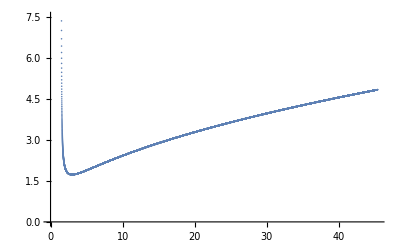

```mathematica
ListPlot@dat
```

```mathematica
Export["datosISCO_2.dat",dat]
```

datosISCO_2.dat

```mathematica
Masa=27.705516915953037;
Mf=(5.31*Masa)/m4*10^-12;(* masas solares *)
Mobj=3*10^9;
NSolve[Mf==Mobj,m4]
```

{{m4→4.90388×10^-20}}

```mathematica
rs=2* Masa/(8*Pi)
```

2.20473

```mathematica
2./(8*Pi)
```

0.0795775

```mathematica
Masa=27.705516915953037;(*3*10^9*)
m=4.90388*10^-1(*10^19 eV*);
Mpunt=2*10^-6 (* Masa Solares * year^-1 *);
i=0;
ri=3.01*rs(*rMin*) (* 6 Masa  *);
σ=5.67×10^-5 (* erg s^-1 cm^-2 K^-4 *);
h=6.6256*10^-27(* erg s *);
kk=1.3805*10^-16(* erg K^-1 *);
νMin=10(*1*10^10*);
νMax=20(*10^18*);
Rout=3.1rs(*50*Masa*)
```

6.83468

```mathematica
(*3.1, 4.1, 5.1, 10.1, 20.1, 30.1, 40.1, 50*)
```

```mathematica
values=N[10^Subdivide[νMin,νMax,400]];

Dat={};
Do[
ν=values[[ii]];
lum=ν fluj[ν,ri];
AppendTo[Dat,{ν,lum}],{ii,1,Length[values]}
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
Export["S1.dat",Dat]
```

S1.dat

```mathematica
Dat
```

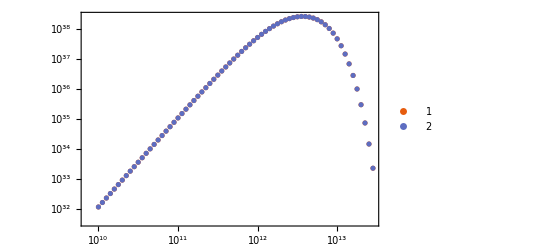

```mathematica
ListLogLogPlot[{Dat[[;;70]],datSch[[;;70]]},PlotLegends->Automatic,PlotTheme->"Scientific"]
```

```mathematica
Export["Schw.dat",datSch]
```

Schw.dat

#### Nuevas fig

```mathematica
ClearAll[Ω,dΩ,EE,L,dL,f,T,fluj,r0,Rout]
```

```mathematica
f[R_?NumberQ,ri_?NumberQ]:=Module[{Rv=N@R,r0=N@ri, dΩ, Ω, EE, L,dL,term, flujo},

ClearAll[flujo,Ω,dΩ,EE,L,dL,term];
Ω[r_]:=Evaluate[(√(r NN[r] NN'[r]))/r/.S[r]];
dΩ[r_]:=Evaluate[(r NN'[r]^2+NN[r] (-NN'[r]+r NN''[r]))/(2 r √(r NN[r] NN'[r]))/.S[r]];
EE[r_]:=Evaluate[NN[r]^2/(√(NN[r] (NN[r]-r NN'[r])))/.S[r]];
L[r_]:=Evaluate[(r √(r NN[r] NN'[r]))/(√(NN[r] (NN[r]-r NN'[r])))/.S[r]];

dL[r_]:=Evaluate[(r NN[r]^2 (-3 r NN'[r]^2+NN[r] (3 NN'[r]+r NN''[r])))/(2 √(r NN[r] NN'[r]) (NN[r] (NN[r]-r NN'[r]))^(3/2))/.S[r]];

term[r_]:=Evaluate[1/(NN[r]gg[r])/.S[r]];

flujo=-1/(4π Rv)(term[Rv])dΩ[Rv]/(EE[Rv]-L[Rv] Ω[Rv])^2 NIntegrate[(EE[rB]-L[rB] Ω[rB])dL[rB],{rB,r0,Rv},Method->{Automatic,"SymbolicProcessing"->0},MaxRecursion->20];

Return[flujo] (* 1/(Mpunt m^2)=rS^2/Mpunt *)
]
```

```mathematica
(* Calculando la temperatura F(R)=σ T(R)^4  *)
```

```mathematica
T[R_?NumberQ,ri_?NumberQ]:= Module[{Rv=N@R,r0=N@ri,Temp},
ClearAll[Temp];
Temp=f[Rv,r0]^(1/4);
Return[Temp] (* (Mpunt m^2)/σ= Mpunt/(σ rS^2)*);
];
```

```mathematica
Mf=(5.31*Masa)/m4*10^-12;(* masas solares *)
Mobj=3*10^9;
```

```mathematica
NSolve[Mf==Mobj,m4]
```

{{m4→2.81589×10^-20}}

```mathematica
rs=(2* Masa[[1]])/(8π)
```

1.266

```mathematica
ri=0.1 (* 3.01*rs *) (* 6 Masa  6 Masa[[1]]/(8*Pi)*);
Rout=300*rs (*50*Masa[[1]] *)(*500rs*)
```

379.799

```mathematica
valuesr=N[10^Subdivide[Log10[ri],Log10[Rout],700]];
```

```mathematica
Datf={};
(*DatT2={};*)
Do[
r=valuesr[[i]];
AppendTo[Datf,{r/rs,f[r,ri]}];
(*AppendTo[DatT2,{r,T[r,ri]}]*),
{i,1,Length[valuesr]}
]
```

```mathematica
Datf2={};
DatT={};
Do[
AppendTo[Datf2,{r,f[r,ri]}];
AppendTo[DatT,{r,T[r,ri]}],
{r,ri,Rout,0.5}
]
```

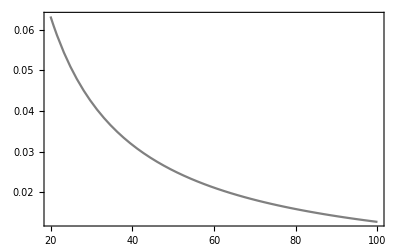

```mathematica
a=Plot[(rs/r),{r,20,100},PlotTheme->"Scientific",PlotStyle->Gray]
```

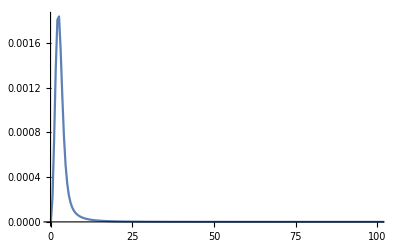

```mathematica
b=ListPlot[Datf,PlotRange->{{0,100},All},Joined->True]
```

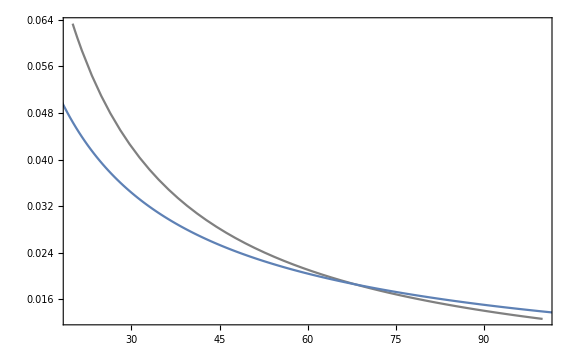

```mathematica
Show[{a,b}]
```

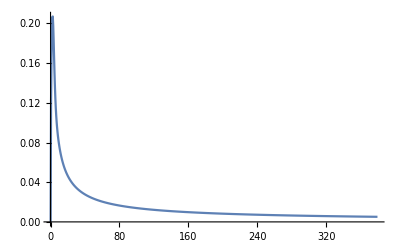

```mathematica
b=ListPlot[DatT,Joined->True,PlotRange->All]
```

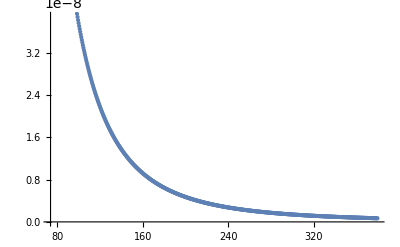

```mathematica
ListPlot@Datf[[-600;;]]
```

```mathematica
n
```

n

```mathematica
3.^(1/4)
```

1.31607

```mathematica
nlm=NonlinearModelFit[Datf[[-500;;]],c(rs^4/x^n),{c,n},x]
```

FittedModel[0.00157077/x^0.740336]

```mathematica
nlm2=NonlinearModelFit[Datf2[[-500;;]], c rs/x^n,{n, c},x]
```

FittedModel[0.0375962/x^2.9992]

```mathematica
nlm2=NonlinearModelFit[Datf2[[-500;;]],c(rs/x)^n,{c,n},x]
```

FittedModel[0.0375962 (1/x)^2.9992]

```mathematica
nlm2["ParameterTable"]
```

General::munfl: Exp[-5005.87] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3650.98] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
n | 2.9992 | 5.83168×10^-6 | 514294. | 0.
c | 0.029697 | 8.77143×10^-7 | 33856.5 | 0.

```mathematica
nlm2["ParameterTable"]
```

General::munfl: Exp[-3674.71] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5005.87] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
c | 0.0185323 | 5.21906×10^-7 | 35508.9 | 0.
n | 2.9992 | 5.83168×10^-6 | 514294. | 0.

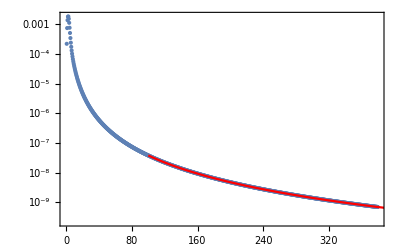

```mathematica
Show[ListLogPlot[Datf2],LogPlot[nlm2[x],{x,100,400},PlotStyle->Red],Frame->True]
```

```mathematica
Export["T_adm_L3_inf.dat",Datf]
```

T_adm_L3_inf.dat

#### Schw2

```mathematica
Quit[]
```

```mathematica
(*interpolando Schw*)
metricSchw={ NN[r]-> √(1-Masa/(4 π r)),  gg[r]-> √((1-Masa/(4 π r))^-1),NN'[r]-> Masa/(8π √(1-Masa/(4π r)) r^2), NN''[r]-> (Masa (3 Masa-16 π r))/(8 √π √(4 π-Masa/r) r^3 (-Masa+4 π r)),gg'[r]-> -(Masa (1/(1-Masa/(4π r)))^(3/2))/(8π r^2)};
```

```mathematica
ClearAll[Ω,dΩ,EE,L,dL,f,T,fluj,r0,Rout]
f[R_?NumberQ,ri_?NumberQ]:=Module[{Rv=N@R,r0=N@ri},

ClearAll[flujo,Ω,dΩ,EE,L,dL,term];
Ω[r_]:=Evaluate[((√(r NN[r] NN'[r]))/r/.metricSchw)//Simplify];
dΩ[r_]:=Evaluate[((r NN'[r]^2+NN[r] (-NN'[r]+r NN''[r]))/(2 r √(r NN[r] NN'[r]))/.metricSchw)//Simplify];
EE[r_]:=Evaluate[(NN[r]^2/(√(NN[r] (NN[r]-r NN'[r])))/.metricSchw)//Simplify];
L[r_]:=Evaluate[((r √(r NN[r] NN'[r]))/(√(NN[r] (NN[r]-r NN'[r])))/.metricSchw)//Simplify];

dL[r_]:=Evaluate[((r NN[r]^2 (-3 r NN'[r]^2+NN[r] (3 NN'[r]+r NN''[r])))/(2 √(r NN[r] NN'[r]) (NN[r] (NN[r]-r NN'[r]))^(3/2))/.metricSchw)//Simplify];

term[r_]:=Evaluate[(1/(NN[r]gg[r])/.metricSchw)//Simplify];

flujo=-1/(4π Rv)(term[Rv])dΩ[Rv]/(EE[Rv]-L[Rv] Ω[Rv])^2 NIntegrate[(EE[rB]-L[rB] Ω[rB])dL[rB],{rB,r0,Rv},Method->{Automatic,"SymbolicProcessing"->0},MaxRecursion->20];

Return[flujo] (* erg s^-1 cm^-2*)
]
(* Calculando la temperatura F(R)=σ T(R)^4  *)
T[R_?NumberQ,ri_?NumberQ]:= Module[{Rv=N@R,r0=N@ri},
ClearAll[Temp];
Temp=f[Rv,r0]^(1/4);
Return[Temp] (*K*);
];
(* Calculando el flujo electromagnético *)
fluj[ν_?NumberQ,ri_?NumberQ]:=Module[{v=N@ν,r0=N@ri},
ClearAll[lumin];
lumin=4.5329*10^-17 ν^3 m^-2 Cos[i]NIntegrate[r/(Exp[(h ν)/(kk T[r,r0])]-1),{r,r0,Rout},MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0}];
Return[lumin]
]
```

```mathematica
Masa=15.932551411870184;
```

```mathematica
(*Masa=27.705516915953037;*)
Mf=(5.31*Masa)/m4*10^-12;(* masas solares *)
Mobj=3*10^9;
NSolve[Mf==Mobj,m4]
```

{{m4→2.82006×10^-20}}

```mathematica
rs=2* Masa/(8*Pi)
```

1.26787

```mathematica
ri= 3.01*rs  (* 6 Masa  6 Masa[[1]]/(8*Pi)*);
Rout=100*rs (*50*Masa[[1]] *)(*500rs*)
```

126.787

```mathematica
valuesr=N[10^Subdivide[Log10[ri],Log10[Rout],700]];
```

```mathematica
Datf={};
(*DatT2={};*)
Do[
r=valuesr[[i]];
AppendTo[Datf,{r/rs,f[r,ri]}];
(*AppendTo[DatT2,{r,T[r,ri]}]*),
{i,1,Length[valuesr]}
]
```

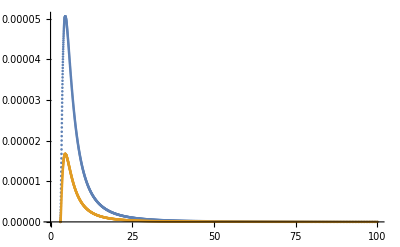

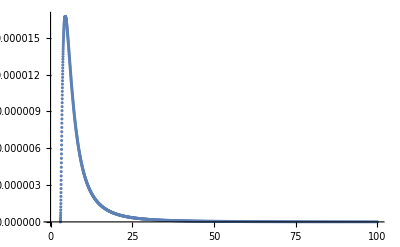

```mathematica
ListPlot[{Datf,Datf2}]
```

```mathematica
Datf2=Datf;
```

```mathematica
Export["Schw2_Ad.dat",Datf]
```

Schw2_Ad.dat